∫(Cos[(2 π t)/(-2^Floor[Log[t]]+2^(1+Floor[Log[t]]))]-Cos[(8 π t)/(-2^Floor[Log[4 t]]+2^(1+Floor[Log[4 t]]))])/(Sin[(2 π t)/(-2^Floor[Log[t]]+2^(1+Floor[Log[t]]))]-Sin[(8 π t)/(-2^Floor[Log[4 t]]+2^(1+Floor[Log[4 t]]))])ⅆt

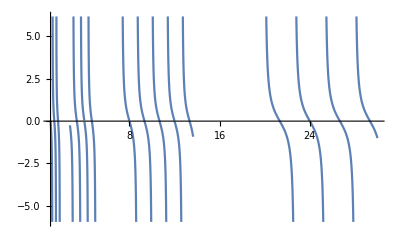

∫(Cos[(2 π t)/(-2^Floor[Log[t]]+2^(1+Floor[Log[t]]))]-Cos[(8 π t)/(-2^Floor[Log[4 t]]+2^(1+Floor[Log[4 t]]))])/(Sin[(2 π t)/(-2^Floor[Log[t]]+2^(1+Floor[Log[t]]))]-Sin[(8 π t)/(-2^Floor[Log[4 t]]+2^(1+Floor[Log[4 t]]))])ⅆt

```mathematica
ClearAll["Global`*"];
rotate[t_]:=(x=-Sin[t];y=Cos[t];{x,y});
deriv[t_,f_,g_]:=-(rotate[2Pi*g[f[t]]][[2]]-rotate[2Pi*g[t]][[2]])/(rotate[2Pi*g[f[t]]][[1]]-rotate[2Pi*g[t]][[1]]);
generateDerivPlot[f_,g_]:= (
start=1;
stop=30;
Plot[deriv[t,f,g],{t,start,stop}]
);
f[n_]:=n*4;
g[n_]:=n/(2^(Floor[Log[n]]+1)-2^Floor[Log[n]]);
integ[t_,f_,g_]:=Integrate[deriv[t,f,g],t];
Print[integ[t,f,g]];
generateDerivPlot[f,g]
Integrate[(Cos[(2 π t)/(-2^Floor[Log[t]]+2^(1+Floor[Log[t]]))]-Cos[(8 π t)/(-2^Floor[Log[4 t]]+2^(1+Floor[Log[4 t]]))])/(Sin[(2 π t)/(-2^Floor[Log[t]]+2^(1+Floor[Log[t]]))]-Sin[(8 π t)/(-2^Floor[Log[4 t]]+2^(1+Floor[Log[4 t]]))]),t]
```